# Programming Tutorial David Meretzky 385-685 8.27.17

## Section 1. Variable Assignment and Built in Functions

```mathematica
(* Inside of the parentheses and stars are comments. Read these before you evaluate the actual code which is in black and blue. *)
```

```mathematica
(* Below, we are assigning a value to a variable x. In this language variables should be named with lower case names.  If we have a variable name with more than one word, you are encouraged to name it by concatenating the two words and capitalizing the second word: secondVariable or firstVariable.  *)

(* Into the variable x, we are placing the value 2.  All of the lines in your program should end in a semi-colon to supress the output and to separate statements. You will get a better feel for their use but for now try to put them at the end of every statement. Evaluate the cell by clicking inside of the cell and using shift and enter together. Notice that before we evaluate the cell, the variable x is blue. 
*)
```

```mathematica
x = 2;
```

```mathematica
(* If you evaluated the cell, x should turn black. This means that the variable now contains a value.*)
```

```mathematica
(* Functions in Mathematica that are a part of the standard library of functions will usually be capitalized. It would be a bad idea to try to use any of these functions as variable names. Evaluate the following code to see the error message.*)
```

```mathematica
Print = 2;
```

Set::wrsym: Symbol Print is Protected.

```mathematica
(* The usual syntax for using functions in Mathematica is:
 Function[arg];
arg is short for argument, which is what programmers call the input of a function. Notice that the argument of the function is surrounded by square brackets which is different from usual mathematical notation which uses parenthesis. 
 Print[x]; returns the value of x to the screen in an output cell. Notice that a new cell is born containing 2.  *)
```

```mathematica
Print[x];
```

2

```mathematica
(* The Print function is smart enough to know not to supress the output even if there is a semi-colon. Notice that if we evaluate the following, we get the same output as Print[x];. Unless the statements are really simple, it is a good habit to just use the print function to print things for now and always use semicolons. *)
```

```mathematica
x
```

2

```mathematica
(* Just like in math we can make use of Mathematica's functions to use x as a replacement for what it contains. Evaluate the next few cells to get a feel for this: *)
```

```mathematica
Print[x + 3];
```

5

```mathematica
x + 3
```

5

```mathematica
Print[x ^ 2]
```

4

```mathematica
Print[x^2 + x + 6]
```

12

```mathematica
Print[x * x]
```

4

```mathematica
(* If we execute the following code we clear the value of the symbol x and then we print it. If you look on the right you will notice that these two statements are both in the same cell. Clicking inside the cell anywhere and pressing shift enter will evaluate all statements from top to bottom. First we clear the value of the variable x, then we print it.  This is our first multi-line cell. In fact most of the time you will have cells that have many things inside of them.  *)
```

```mathematica
Clear[x];
Print[x];
```

x

```mathematica
(* Now what happens if we evaluate the previous string of familiar computations on x?  *)
```

```mathematica
Print[x + 3];
```

3+x

```mathematica
x + 3
```

3+x

```mathematica
Print[x ^ 2]
```

x^2

```mathematica
Print[x^2 + x + 6]
```

6+x+x^2

```mathematica
x * x
```

x^2

```mathematica
(* We also have examples of some more exciting functions: Log, Cos, Sin. We are also given values for familiar mathematical constants like Pi, E, and I. Notice that they are capitalized. Dont try to use them as variables. Use them for what they are, numbers of different sorts. *)
```

```mathematica
Cos[1/4*Pi]
```

1/(√2)

```mathematica
Log[E]
```

1

```mathematica
I^2
```

-1

```mathematica
(* N is a function that returns the numerical values of the first argument to the degree of precision as specified by it's second argument. If a function has more than one argument, they will be seperated by commas.  *)
```

```mathematica
N[E, 1]
```

3.

```mathematica
N[E, 2]
```

2.7

```mathematica
N[E, 5]
```

2.7183

```mathematica
N[E, 10]
```

2.718281828

```mathematica
N[E, 100]
```

2.718281828459045235360287471352662497757247093699959574966967627724076630353547594571382178525166427

```mathematica
(* You should be able to guess what the function D does based on its output and arguments. Here I am creating a second degree polynomial out of the unassigned variable x, and putting it into the variable poly1. *)
```

```mathematica
poly1 = x^2 + x + 6;
D[poly1, x]
```

1+2 x

```mathematica
(* There! We have successfully differentiated a symbolic expression! Symbolic manipulation and computation is one of Mathematica's strong suits. (If you play around in the Demonstrations and Documentation that we talked about in class see if you can figure out how to use the functions that will compute limits for you.) You may have guessed just now that D is the differentiation function who's second argument is the variable we are differentiating with respect to. To quote Ron Swanson: You'd be right.  

Now what happens if we say: *)
```

```mathematica
x = 2;
poly1 = x^2 + x + 6;
D[poly1, x]
```

General::ivar: 2 is not a valid variable.

∂_2 12

### Forensics

```mathematica
(* We got an error message. You should be asking at this point: Why did we get an error? Should we not have just gotten 0 by differentiating 12  (the value of that polynomial at 2) with respect to x?  

In this case the first thing we have done is to assign x the value 2. Our poly variable then is holding the value of the expression x^2 + x + 6 which is equal to 12. Then on the 3rd line we ask mathematica to differentiate with respect to x which again is just 2. so we are equivaluently saying: *)
```

```mathematica
D[12,2]
```

General::ivar: 2 is not a valid variable.

∂_2 12

### A note on types:

```mathematica
(* If something is going wrong for you. See if you can follow the logic and values of the variables at each step in the program. What may help you the most is to break up the cell into multiple cells and evaluate each one at a time to figure out where you have gone wrong exactly. 90% of the errors will come from putting something of the wrong data type into a function or scenario which calls for a different type. The Head function will tell you what the data type of its argument is.*)
Head[4]
```

Integer

```mathematica
Head[1/4]
```

Rational

```mathematica
Head[4.0]
```

Real

```mathematica
Head[4+4*I]
```

Complex

```mathematica
Head[a^3]
```

Integer

```mathematica
(* You wont need to use Head all the time but it is good to be aware that types exist. Mismatched types will be a source of errors in your program (errors in your program are also known as bugs). 


In addition to creating variables that hold integers or reals or complex numbers, there are other things a variable can hold.  To name a few, they can hold booleans (named for the logician George Boole), strings (short for strings of characters), lists (containers, essentially tuples, that may hold other things inside of them). You could even have lists containing lists. This is how (in this language) we will describe matricies.*)
```

```mathematica
(* Here is an example of a string of characters vs a variable name. They are enclosed in quotes. My dear Eliza, We can type plain english as strings! (This is an example from another George B.'s book titled Pygmalion)*)
```

```mathematica
x = 2;
```

```mathematica
Print[x];
```

2

```mathematica
Head[x]
```

Integer

```mathematica
Print["x"];
```

x

```mathematica
Head["x"]
```

String

```mathematica
Head["The rain in Spain falls mainly on the planes."]
```

String

## Section 2. Booleans and If statements

```mathematica
(* Booleans are truth values. True and False are built in values much the same way Pi and E, or 1, or 2,or 3 are.    There are comparison operators  < and > that return True or False. They are, in a sense, questions. What are some questions we can ask about numbers? *)
```

```mathematica
1 < 2
```

True

```mathematica
4 < 3
```

False

```mathematica
(* Slightly more complex, *)
```

```mathematica
1/Sqrt[n+3] > 1/Sqrt[4*n]
```

False

```mathematica
(* Use reduce to see for what n the expression is true:  (In fact it misses one value, the computers are quite up to us yet I guess. )*)
```

```mathematica
Reduce[1/(√(3+n))>1/(2 √n)]
```

False

```mathematica
(* We are putting True into the variable t, and False into the variable f: *)
```

```mathematica
t = 1 < 2;
```

```mathematica
f = 1 > 2;
```

```mathematica
Print[t]
```

True

```mathematica
(* The logical "OR" and "AND" and "NOT" operators are ||, &&, and ! respectively. *)
```

```mathematica
t || f
```

True

```mathematica
t && f
```

False

```mathematica
(* Not True *)
```

```mathematica
!t
```

False

```mathematica
(* Not False *)
```

```mathematica
!f
```

True

```mathematica
(* equals equals == is another comparison operator like < or >. 
a == b means "is a equal to b? " and will return True or False *)
```

```mathematica
4 == 5
```

False

```mathematica
4 == 4
```

True

```mathematica
t == !f
```

True

### If Statements

```mathematica
(* We are now ready for our first control structure. So far whenever we have evaluated a cell, the whole cell was evaluated top to bottom end of story. In the following cell, we will create a variable i, and then set i equal to itself plus 3 . This looks mathematically wrongity wrong wrong. But it is in fact a valid statement. i == i + 3 is evaluates to False.  *)
```

```mathematica
i = 2;        (* on this line i = 2*)
i = i + 3;  (* on this line we are adding one to i*)
Print[i];

(* Finally we print out the desired 5 *)
```

5

```mathematica
(* Suppose now that we didn't always want to add one to i whenever we arrive at the second line of the program. An If statement will test a condition, and based on the truth of the condition evaluate some further expression. The first argument of If is the test condition. If the test condition evaluates to False, the code in the second argument is executed (this is called the body of the If statement). If the test condition evaluates to False, then the second argument is skipped. This is called an If Else Statement. In fact the third argument is optional. If you only have the If statement, and no else statement, you should only have one comma seperating the condition and the body.  *)
```

```mathematica
If[1 <2, Print["Condition is True"], Print["Condition is False"]];
```

Condition is True

```mathematica
(* I know that that one was not, but standard practise is to put the condition, body, and else all on seperate lines. As shown below: *)
```

```mathematica
If[1 <2,
 Print["Condition is True"],
 Print["Condition is False"]
];
```

Condition is True

```mathematica
(* Indeed 1 is less than 2 so the body is evaluated and the else is skipped. *)
```

```mathematica
(*Note that True and False evaluate to True and False, so if we leave these as the conditions (or variables containing them),    they will work accordingly. *)
False
```

False

```mathematica
True
```

True

```mathematica
If[True,
 Print["Condition is True"],
 Print["Condition is False"]
];
```

Condition is True

```mathematica
If[False,
 Print["Condition is True"],
 Print["Condition is False"]
];
```

Condition is False

```mathematica
(* Here I am putting True into t, then negating t as the condition so it evaluates to False.*)
```

```mathematica
t = True;
If[!t,
 Print["Condition is True"],
 Print["Condition is False"]
];
```

Condition is False

```mathematica
(* Lets go back to incrementing i. Now instead of just printing a string, we will do something to a variable depending on the truth value of the condition. Here if i is less than 5 we will add 5 to i and reset i with this new higher value.*)
```

```mathematica
i = 2;
```

```mathematica
If[i <5,
 i = i + 3
];
```

```mathematica
Print[i];
```

5

```mathematica
(* Now I has the value 5. Notice that we have no else body. 

Lets do this again. This time we will have more than one statement in the body of the If.*)
```

```mathematica
i = 2;
```

```mathematica
If[i <5,
 i = i + 3;
Print[i];
];
```

5

```mathematica
(* Notice a few things are different. I put a semi colon at the end of the incrementing line where we change i. This is to seperate the increment statement from the print statement. Suppose we forgot to put this semi-colon:*)
```

```mathematica
i = 2;
```

```mathematica
If[i <5,
 i = i + 3
Print[i];
];
```

2

```mathematica
Print[i]
```

2+3 Null

### Forensics

```mathematica
(* Where there is empty space Mathematica is filling in a multiplication. Here is our first example of type mismatch. Lets take this piece by piece. 

Mathematica correctly evaluates i < 5 to True.

then it sees:
 
i = i + 3
Print[i];

    this is identically:

i = i + 3Print[i];

and it tries to multiply 3 times the print statment. This crashes and burns and returns a Null value. Null is the empty data type. We are left with 2 + 3Null.  
*)


(* In almost every program you write this semester you will use if statements. If statements are powerful. Writing programs that have more than one line is also powerful. But with great power comes great responsibility. Do not forget semicolons.

In our final example of If statements we will Nest them: Suppose that we are making a peanut butter and jelly sandwich. *)
```

```mathematica
peanutButter = False;
jelly = False;
```

```mathematica
If[peanutButter == True,
If[jelly == True,
Print["Nice job, it looks like you have a good sandwich."],
Print["Ok, you're a serious fellow I can tell because your sandwich has no jelly on it but it does have peanut butter."]
];
, (* below this comma is evaluated in the case peanut butter is false *)
If[jelly == True,
Print["Ok, you're a serious fellow I can tell because your sandwich has no peanut butter on it but it does have jelly."],
Print["This is a bread sandwich."]
];
];
```

This is a bread sandwich.

```mathematica
If[peanutButter == True,
(* We are now in the body of the if where there is peanutButter on the sandwich
is there also jelly?*)
If[jelly == True,
(* We are now in the body of the if where there is peanutButter on the sandwich
and there is also jelly, in this case: *)
Print["Nice job, it looks like you have a good sandwich."]
,
(* We are now in the body of the if where there is peanutButter on the sandwich
but no jelly in this case: *)
Print["Ok, you're a serious fellow I can tell because your sandwich has no jelly on it but it does have peanut butter."]
];
,
(* We are now past the second comma, cheese is false and we have skipped the entire body where we would go if peanutButter we true,
is there also jelly? *)
If[jelly == True,
(* We are now in the body of the if where there is no peanutButter on the sandiwich
but there is  jelly*)
Print["Ok, you're a serious fellow I can tell because your sandwich has no peanut butter on it but it does have jelly."]
,
(* We are now in the place of no peanutButter and no jelly*)
Print["This is a bread sandwich."]
];
];
```

This is a bread sandwich.

## Section 3. Lists, and Lists of Lists, and Lists of Lists of Lists, and so on...

```mathematica
(* Lists in this language are tuples seperated by commas surrounded by curly braces:*)
```

```mathematica
l1 = {10,20,30,40};
```

```mathematica
(* l1 is a variable containing a list of the multiples of 10 from 10 to 40. Min and Max are functions that can be applied to lists*)
```

```mathematica
Max[{10,20,30,40}]
```

40

```mathematica
Min[l1]
```

10

```mathematica
(* Mean and Total are functions that compute the Mean value of the list, and the sum total of the elements of the list.*)
```

```mathematica
Total[l1]
```

100

```mathematica
Mean[l1]
```

25

```mathematica
(* In the same way that we could increment a number with the following syntax*)
```

```mathematica
i = 1;
```

```mathematica
i = i + 1;
```

```mathematica
i
```

2

```mathematica
(* we can add things to lists *)
```

```mathematica
l2 = {True, 10, 1.5, I};
```

```mathematica
l2 = Append[l2, "Friday"];
```

```mathematica
l2
```

{True,10,1.5,ⅈ,Friday}

```mathematica
(* Here we have appended to the list l2, the string "Friday". This example is meant to show that lists in general may hold different data types. If we try to check what these data types are we might think of trying to apply Head which infuriatingly gives us exactly what we asked for: *)

Head[l2]
```

List

```mathematica
(* However we may use the map function to map head over all of the elements of the list. Map takes as its first argument a function and as its second a list to which that function will be mapped. Dont use this. When we go over loops you will see a better way to do this for now. *)
```

```mathematica
Map[Head, l2]
```

{Symbol,Integer,Real,Complex,String}

### Wherever possible, i.e. within the limits of your own sanity, do not use Mathematica’s fancy built in functions for high level things. Map is an example, do not use Map. AppendTo is fine. Mean can be easily constructed out of total using Length. When we do loops we will see how to build our own Totals and Lengths. If I ask you to write a program to perform Lagrange Interpolation you will not get credit if you hand in a one line program that says LagrangeInterpolation[pointSet] using Mathematica’s gigantic standard library. This does not count as you doing the assignment.

```mathematica
Total[l1]/Length[l1] == Mean[l1]
```

True

```mathematica
(* Ok, time for lists of lists.  *)

lofl = {};
AppendTo[lofl, {20,30,40}];
```

```mathematica
lofl
```

{{20,30,40}}

```mathematica
AppendTo[lofl, {20,30,40}];
```

```mathematica
lofl
```

{{20,30,40},{20,30,40}}

```mathematica
AppendTo[lofl, {20,30,40}];
```

```mathematica
lofl
```

{{20,30,40},{20,30,40},{20,30,40}}

### Good practice note: Notice that I had to type the same identical thing 3 times. If you find yourself typing the same thing over and over and over and over, your program may run, it may give you good output but stop, take a break, come back to it. There is always a simpler way which will let you avoid typing repetitive things, you will think of it. Right now we do not have the machinery to do that in this case but we will shortly.

```mathematica
(* Ok now i have a list of lists. Lets see it as a Matrix: Note: MatrixForm is just for displaying the data. If I ask you to hand in a matrix as homework it should be in matrix form. All matricies again are just lists of lists in this language.*)
MatrixForm[lofl]
```

(20 | 30 | 40
20 | 30 | 40
20 | 30 | 40)

```mathematica
(* Looking back at the variable lofl*)
```

```mathematica
lofl
```

{{20,30,40},{20,30,40},{20,30,40}}

```mathematica
(* It is still thankfully just a list of lists. How do we access parts of the list? Suppose I wanted to turn the diagonals into 10* their current selves? Part[A, i] gives me the ith entry of the list A. in this case it gives me the first list for i = 1.  *)
i = 1;
Part[lofl, i]
```

{20,30,40}

```mathematica
(* Suppose I just wanted the first entry of the first list I could say: *)
i = 1;
j = 1;
Part[Part[lofl, i], j]
```

20

### Again, If you find yourself typing the same thing over and over and over and over, your program may run, it may give you good output but stop take a break come back to it. There is always a simpler way which will let you avoid typing repetitive things (recall our sandwich shop if statement):

```mathematica
(* In this case we can replace the above syntax with: *)
i = 1;
j = 1;
Part[lofl, i, j]
```

20

```mathematica
(* In fact there is a better short hand for lists: double brackets after the list will give you the 
ith element and then the jth element of the ith element. *)
lofl[[i]]
```

{20,30,40}

```mathematica
lofl[[i]][[j]]
```

20

```mathematica
(*Further tools:  the double semi-colon will give you start and stop indicies to take from *)
```

```mathematica
lofl[[i]][[j;;j+1]]
```

{20,30}

```mathematica
(* The following doesnt give us what we would expect: *)
```

```mathematica
lofl[[i;;i +1]][[j;;j+1]]
```

{{20,30,40},{20,30,40}}

```mathematica
(*we instead say: *)
```

```mathematica
lofl[[i;;i +1,j;;j+1]]
```

{{20,30},{20,30}}

```mathematica
(*Recall *)
```

```mathematica
l2
```

{True,10,1.5,ⅈ,Friday}

```mathematica
(* Begining through entry 2*)
```

```mathematica
l2[[;;2]]
```

{True,10}

```mathematica
(* every second entry*)
```

```mathematica
l2[[;;;;2]]
```

{True,1.5,Friday}

```mathematica
(* every third entry*)
```

```mathematica
l2[[;;;;3]]
```

{True,ⅈ}

## Section 4. For and While

```mathematica
(* So far I have made such a big fuss about there being no need to write the same thing over and over. Wow I keep saying this. I should take my own advice but I can't stress this strongly enough. So here is the real machinery: *)
```

```mathematica
For[i = 1, i ≤ 10, i = i + 1, Print[i]];
```

1

2

3

4

5

6

7

8

9

10

```mathematica
(*  For is a looping mechanism. It is a function with four arguments. Its first 3 arguments specify when and if the fourth argument should be executed and how many times.    Lets take a look at the last argument first:
Print[i]. This is the body of the For loop, this is where the major statement or collection of statements goes. 
Usually when we write a for loop, the first 3 lines go on the same line seperated by commas and the body which usually has many statements gets multiple lines like an If statement.

The first argument of the For loop is always executed. It is only executed once at the very begining. Then the following things occur. The second, fourth and then 3rd arguments are executed in that order. They are called the test, body, and incrementation.

In this case the test is the statement: is i less than or equal to 10?  i ≤ 10  
(this symbol ≤ (analogously ≥)  is generated by typing a < and then a = next to each other). 

If the test evaluates to true, the fourth argument, the body, is executed, in this case just the simple print statement,

Finally the 3rd statement i = i + 1 is executed to increment i. 

Initially we have 1. Then we check 1 ≤ 10, this is true, we execute the body and print i, which is 1. then we add one to i and update i, at this point we execute another check, 2 ≤ 10? this is true we execute the body and print i, which is 2. then we increment i, 
at this point we go around and around the (maybe its now clear why we call it a loop) loop, until finally we have printed 10, we then increment to 11, and 11 is not less than or equal to 10.  11 ≤ 10 evaluates to False, at which point we exit the loop. For drops us out at the bottom of the loop. 

Note: ++i, and i += 1 are both shorthand for i = i + 1. 

                 *)
```

```mathematica
++i
```

12

```mathematica
(* What could we do over and over? *)
```

```mathematica
l2
```

{True,10,1.5,ⅈ,Friday}

```mathematica
Length[l2]
```

5

```mathematica
(* We are going to iterate over a list using a for loop. In the body of the for loop the value of the iterator is used to take the part of l2. We then print it out. *)
```

```mathematica
For[i = 1, i ≤ Length[l2], ++i, 
Print[
l2[[i]]
];
];
```

True

10

1.5

ⅈ

Friday

```mathematica
(* Let's alter a list: *)
```

```mathematica
a = {1,1,1,2,2,2};
```

```mathematica
For[i =1, i ≤ Length[a], ++i, 
++a[[i]]
];
```

```mathematica
a
```

{2,2,2,3,3,3}

```mathematica
(* Lets make a 10 by 10 identity matrix: *)
```

```mathematica
id = {};
```

```mathematica
For[i = 1, i ≤ 10, ++i,
(* 
We are going to add 10 new rows to id. One row will be added each time around the outter loop.
Inside the inner loop we will populate each row with the correct elements. This will involve adding nine zero's and one one. 
*)
newrow = {};

For[j = 1, j ≤ 10, ++j,
If[j == i, (*  if i == j we should append to the newrow a 1 otherwise it gets a 0. *)
 AppendTo[newrow, 1],
AppendTo[newrow, 0]
]; (* end If *)
]; (* end j loop*)


(*finally we append the row to the list id*)
AppendTo[id, newrow];

]; (*end i loop*)
```

```mathematica
MatrixForm[id]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* Lets make a while loop. This is simpler but more dangerous than a For loop. There are no Iterators. While takes two arguments, a test condition and a body. It evaluates this pair infinitely as long as the test condition is true. *)
```

```mathematica
i = 1;
While[i ≤ 5, 
 Print[i];
++i;
];
```

1

2

3

4

5

```mathematica
(*Note the difference in output if we switch the increment and the print. *)
```

```mathematica
i = 1;
While[i ≤ 5, 
++i;
 Print[i];
];
```

2

3

4

5

6

```mathematica
(* When would you use a while loop? 

How about when you dont know exactly how many iterations your loop will take to get its answer. In this case you would want to use a while loop so that you dont run for too long or too short. *)
```

```mathematica
(* Suppose we had a loop that kept going based on two conditions. Then the test expression could be a little more complicated. Here our test condition says keep going when: a≤ 5 or b ≤ 10. *)
```

```mathematica
a = 1;
b = 1;
While[a <= 5 || b <= 10, 
Print["New step"];
Print["a == ",a];
Print["b == ", b];
Print["a * b == ",a * b];
a = a+1;
b = 2*b;
];
```

New step

a == 1

b == 1

a * b == 1

New step

a == 2

b == 2

a * b == 4

New step

a == 3

b == 4

a * b == 12

New step

a == 4

b == 8

a * b == 32

New step

a == 5

b == 16

a * b == 80

```mathematica
(* Suppose we wanted to know how many times we went around the while loop? We could initialize a variable with 1, then add one to the variable every time we go around the while loop. In this way after the loop ends we could ask, how many times we went around by just looking inside this variable.*)

counter = 0;
a = 1;
b = 1;
While[a <= 5 || b <= 10, 
counter = counter + 1;
Print["a * b == ",a * b];
a = a+1;
b = 2*b;
];
Print["We went around the while loop exactly ", counter," times"]
```

a * b == 1

a * b == 4

a * b == 12

a * b == 32

a * b == 80

We went around the while loop exactly 5 times

```mathematica
(* A while loop can run forever: This can happen when the test condition always evaluates to true. *)
```

### WARNING: While loops can be dangerous IF YOU ARE STUCK IN AN INFINITE LOOP: Go to the menu tab and select Evaluation -> Quit Kernel -> Local This will stop the program in it’s tracks and clear all variables of their values. From black to blue all the symbols go. After you have finished coding and before you hand something in to me: Follow the above instructions to quit the kernel. Then reevaluate your whole program to make sure that your program runs smoothly.

## Section 5. User defined functions

```mathematica
(* So far we have seen many functions that were created as part of the language, built-ins so they call them. How could we make our own? In this language 

f(x) = x^2

is written as:

*)
```

```mathematica
Clear[f];
```

```mathematica
f[x_] := x^2;
```

```mathematica
f[2]
```

4

```mathematica
(* Don't forget the underscore when declaring what arguments the function will take. 

Halfway through the program if you are going to change the function then define the function without the semi colon *)
```

```mathematica
f[x_] = x^2;
```

```mathematica
f[2]
```

4

```mathematica
(* Please also try to use the colon when we define functions based on other functions we will not use the := . *)
```

```mathematica
(* Here we define a function g of several variables, and then we define a function h in terms of g. *)
```

```mathematica
g[x_, y_] := x^2 + 2*x*y + y^2;
```

```mathematica
h[x_] := g[x,2];
```

```mathematica
(* Use Plot and Plot3D respectively for functions of one or two variables.*)
```

```mathematica
Plot3D[g[x,y], {x, -5,5},{y,-5,5}]
```

-Graphics3D-

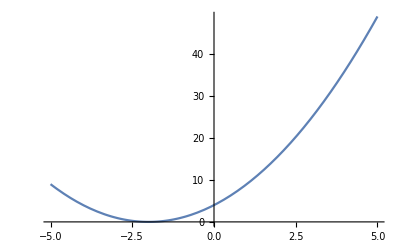

```mathematica
Plot[h[x], {x, -5,5}]
```

```mathematica
(* We can also apply functions to lists:  first I am building up a list: *)
```

```mathematica
l = {};
```

```mathematica
For[i = -5, i ≤ 5, ++i,
AppendTo[l, i];
]
```

```mathematica
l
```

{-5,-4,-3,-2,-1,0,1,2,3,4,5}

```mathematica
(* We will now apply h to the list: *)
```

```mathematica
h[l]
```

{9,4,1,0,1,4,9,16,25,36,49}

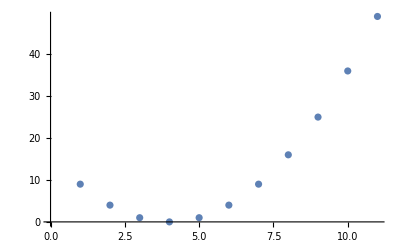

```mathematica
ListPlot[h[l]]
```

```mathematica
(* We will Define a Family of Functions:  This will be useful when we program methods of interpolating functions.
Notice the Subscript:

*)

plotlist = {};
For[i = 1, i ≤ 5, ++i,
Subscript[f, i][x_] := h[i] * x^2 + i * x + i;
AppendTo[plotlist, Plot[Subscript[f, i][x], {x,0,5}]];
];
```

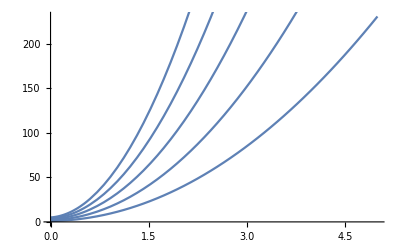

```mathematica
Show[plotlist]
```

## Section 6. Error

```mathematica
(*  When Pandora opened the box of all of the horrible computational errors in the universe, many types of error sprang out. To name a few: Type 1, Type 2, systemic error, roundoff error, compound error. Lets talk about some of these.

When we program Gauss Jordan elimination: you will see that a small error in the top left hand corner of the matrix will propagate through the entirety of our comptuations compounding itself in the bottom right. The larger the matrix the larger the error.  When you type your less than the wrong way in the test condition of a while loop and you spiral off into an infinite oblivion of Print statements this is an example of an error in logic or a systemic error. When we approximate a function, or its integral, or its derivative we are going to have some error by virtue of the fact that we are looking for an approximation. However, approximations wouldnt be of very much use to us unless we had some method for bounding the error. *)
```

```mathematica
(* suppose we know the function f(1) = 1, and f(1.1) = 1.21; We could then use Newton's quotient to estimate the value of the derivative at the point 1. *)
```

```mathematica
a = 1;
b = 1.1;
fa = 1;
fb = 1.21;
```

```mathematica
estd = (fb - fa)/ (b -a);
```

```mathematica
Print[estd]
```

2.1

```mathematica
(* this is our estimate for the derivative of the function at 1.*)
```

```mathematica
(* In fact, our function is *)
```

```mathematica
f[x_] := x^2;
```

```mathematica
g[y_] = D[f[y],y];
```

```mathematica
g[1]
```

2

```mathematica
(* to do this correctly we omit the second colon in the definition of g *)
```

```mathematica
(* See the definition of error, absolute error, relative error ,relative absolute error. from class notes*)
```

```mathematica
e =g[1] - estd
```

-0.1

```mathematica
absoluteError = Abs[e]
```

0.1

```mathematica
relativeError = e/g[1]
```

-0.05

```mathematica
relativeAbsError = Abs[relativeError]
```

0.05

#### Homework Due Wednesday September 6th: For these exercises you will need to define functions f and g. If you can: Use a For loop to compute the error for each value of x. You will have an expression like 10^(-i) somewhere in the body of the For loop. Append the error to a list, then print the list and plot the list using ListPlot.

#### Additionally: Write a program that plots the iteration counts for each number from 1 to a few thousand (of your choice). Some number high enough that it doesn’t take forever to run but so that you get something interesting. Begin by writing a while loop that plays the game for a single number. Once this code works, use a For loop to make your program run this while loop a number of times. You can find the rules here: https://en.wikipedia.org/wiki/Collatz_conjecture The final structure of the program should look something like this: list = {}; For[i = 1, i <= 1000, ++i, n = i; count = 0; Play the Collatz game starting with n, counting the number of steps it takes to finish, use a while loop append count to list ]; ListPlot[list]; IntegerQ may be a helpful function...